```mathematica
ds=r (s+ia+ic+iam+icm)(1-(s+ia+ic+iam+icm)/K)-β[v] s (ia+ic)+γ ia-β[vm] s (iam+icm)+γ iam-μ s;
dia=p β[v] s (ia+ic)-(v+γ+μ) ia;
dic=(1-p) β[v] s (ia+ic)-(v+μ) ic;
diam=p β[vm] s (iam+icm)-(vm+γ+μ) iam;
dicm=(1-p) β[vm] s (iam+icm)-(vm+μ) icm;
```

```mathematica
J=D[{ds,dia,dic,diam,dicm},{{s,ia,ic,iam,icm}}]/.{iam->0,icm->0};
MatrixForm[J]
```

(-(r (ia+ic+s))/K+r (1-(ia+ic+s)/K)-μ-(ia+ic) β[v] | -(r (ia+ic+s))/K+r (1-(ia+ic+s)/K)+γ-s β[v] | -(r (ia+ic+s))/K+r (1-(ia+ic+s)/K)-s β[v] | -(r (ia+ic+s))/K+r (1-(ia+ic+s)/K)+γ-s β[vm] | -(r (ia+ic+s))/K+r (1-(ia+ic+s)/K)-s β[vm]
(ia+ic) p β[v] | -v-γ-μ+p s β[v] | p s β[v] | 0 | 0
(ia+ic) (1-p) β[v] | (1-p) s β[v] | -v-μ+(1-p) s β[v] | 0 | 0
0 | 0 | 0 | -vm-γ-μ+p s β[vm] | p s β[vm]
0 | 0 | 0 | (1-p) s β[vm] | -vm-μ+(1-p) s β[vm])

```mathematica
(* Use NGM to find the invasion fitness for the bottom right submatrix*)
```

```mathematica
F={{s p β[vm],s p β[vm]},{s (1-p) β[vm],s (1-p) β[vm]}};
V={{vm+γ+μ,0},{0,vm+μ}};
J[[4;;5,4;;5]]==F-V
Eigenvalues[-V] (* must be negative *)
Inverse[V] (* must be non-negative *)
Eigenvalues[F.Inverse[V]]
```

True

{-vm-μ,-vm-γ-μ}

{{1/(vm+γ+μ),0},{0,1/(vm+μ)}}

{0,(s (vm+γ-p γ+μ) β[vm])/((vm+μ) (vm+γ+μ))}

```mathematica
(* Mutant can invade if (s (vm+γ-p γ+μ) β[vm])/((vm+μ) (vm+γ+μ)) > 1 *)
```

```mathematica
Simplify[(p β[vm]S)/(vm+γ+μ)+((1-p) β[vm]S)/(vm+μ)]
```

(S (vm+γ-p γ+μ) β[vm])/((vm+μ) (vm+γ+μ))

```mathematica
(* Fitness gradient *)
FitGrad=Simplify[D[(s (vm+γ-p γ+μ) β[vm])/((vm+μ) (vm+γ+μ)),vm]]
```

1/((vm+μ)^2 (vm+γ+μ)^2)s ((vm+μ) (vm+γ+μ) β[vm]-(vm+μ) (vm+γ-p γ+μ) β[vm]-(vm+γ+μ) (vm+γ-p γ+μ) β[vm]+(vm+μ) (vm+γ+μ) (vm+γ-p γ+μ) β'[vm])

```mathematica
(* ESS condition - as long as β''(Subscript[v, m]) < 0, this should be negative, satisfying the condition for evolutionary stability *)
D[(s (vm+γ-p γ+μ) β[vm])/((vm+μ) (vm+γ+μ)),{vm,2}]/.{Solve[D[(s (vm+γ-p γ+μ) β[vm])/((vm+μ) (vm+γ+μ)),vm]==0,β'[vm]]}//Simplify
```

{{(s (-2 (-1+p) p γ^2 β[vm]+(vm+μ) (vm+γ+μ) (vm+γ-p γ+μ)^2 β''[vm]))/((vm+μ)^2 (vm+γ+μ)^2 (vm+γ-p γ+μ))}}

```mathematica
(* ESS virulence solves *)
Simplify[D[(s (vm+γ-p γ+μ) β[vm])/((vm+μ) (vm+γ+μ))/.β[vm]->β0 vm/(h+vm),vm]]
```

(s β0 (-vm^4+2 vm^3 ((-1+p) γ-μ)+2 h vm μ (γ+μ)-h ((-1+p) γ-μ) μ (γ+μ)+vm^2 ((-1+p) γ^2+2 (-1+p) γ μ-μ^2+h (p γ+μ))))/((h+vm)^2 (vm+μ)^2 (vm+γ+μ)^2)

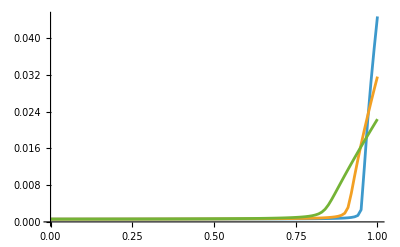

```mathematica
ESS5=Table[{pp,Solve[((-vm^4+2 vm^3 ((-1+p) γ-μ)+2 h vm μ (γ+μ)-h ((-1+p) γ-μ) μ (γ+μ)+vm^2 ((-1+p) γ^2+2 (-1+p) γ μ-μ^2+h (p γ+μ)))/.{h->0.01,μ->1/(75*365),γ->1/5,p->pp})==0,vm][[4,1,2]]},{pp,0,1,0.01}];
ESS10=Table[{pp,Solve[((-vm^4+2 vm^3 ((-1+p) γ-μ)+2 h vm μ (γ+μ)-h ((-1+p) γ-μ) μ (γ+μ)+vm^2 ((-1+p) γ^2+2 (-1+p) γ μ-μ^2+h (p γ+μ)))/.{h->0.01,μ->1/(75*365),γ->1/10,p->pp})==0,vm][[4,1,2]]},{pp,0,1,0.01}];
ESS20=Table[{pp,Solve[((-vm^4+2 vm^3 ((-1+p) γ-μ)+2 h vm μ (γ+μ)-h ((-1+p) γ-μ) μ (γ+μ)+vm^2 ((-1+p) γ^2+2 (-1+p) γ μ-μ^2+h (p γ+μ)))/.{h->0.01,μ->1/(75*365),γ->1/20,p->pp})==0,vm][[4,1,2]]},{pp,0,1,0.01}];
ListLinePlot[{ESS5,ESS10,ESS20},PlotRange->All]
```

```mathematica
Export["Fig5_ESS_5.csv",ESS5];
Export["Fig5_ESS_10.csv",ESS10];
Export["Fig5_ESS_20.csv",ESS20];
```

Find the ESS as recovery rate is varied when either p = 1 or p = 0.

```mathematica
ESS1=Table[{pp,Solve[((-vm^4+2 vm^3 ((-1+p) γ-μ)+2 h vm μ (γ+μ)-h ((-1+p) γ-μ) μ (γ+μ)+vm^2 ((-1+p) γ^2+2 (-1+p) γ μ-μ^2+h (p γ+μ)))/.{h->0.01,μ->1/(75*365),γ->pp,p->1})==0,vm][[4,1,2]]},{pp,0,0.2,0.0025}];
ESS0=Table[{pp,Solve[((-vm^4+2 vm^3 ((-1+p) γ-μ)+2 h vm μ (γ+μ)-h ((-1+p) γ-μ) μ (γ+μ)+vm^2 ((-1+p) γ^2+2 (-1+p) γ μ-μ^2+h (p γ+μ)))/.{h->0.01,μ->1/(75*365),γ->pp,p->0})==0,vm][[4,1,2]]},{pp,0,0.2,0.0025}];
```

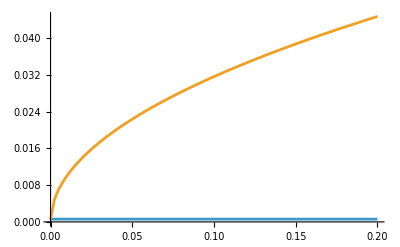

```mathematica
ListLinePlot[{ESS0,ESS1}]
```

```mathematica
Export["Fig5_ESS_baseline_p=1.csv",ESS1];
Export["Fig5_ESS_baseline_p=0.csv",ESS0];
```

```mathematica
N[1/(75*365)]
```

0.0000365297